# Data Science and Machine Learning

## Assignment 1: Manipulating, cleaning, visualizing data

In this assignment, we will use a dataset to perform cleaning and visualization operations.
We will first use clean data from company entities.
Then, we will use a dataset about the performance of several companies across different years. The performance is shown in terms of different social, environmental, and governance scores. For each company, the dataset also contains a set of features, e.g, market value, assets, etc.
Once you are done you have to:
       1. Submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1159929
       2. Answer the questions to the quiz: https://moodle.epfl.ch/mod/quiz/view.php?id=1171854
You have to do both. The answers to the quiz should be supported by your code. If they are not you will not receive the point for it. 
If there is need for further clarifications on the questions, after the assignment is released, we will update this file, so make sure you check the git repository for updates.
	Good luck!

## Warm-Up (..the clean data...)

For the companies: {"Zoom Video Communications","Apple","Biogen","Amazon","Adobe","Invesco Ltd","Facebook","Microsoft"}, create a data structure containing their "CurrentAssets".
Your structure should be an association with keys being company entities.

MATHIEU

```mathematica
CurrentAss = EntityValue[{Entity["Company","ZoomVideoCommunications::3y89f"],Entity["Company","Apple::5zkjq"],Entity["Company","BiogenIdec::gc6p2"],Entity["Company","AmazonDotCom::bt233"],Entity["Company","AdobeSystems::hp28c"],Entity["Company","Invesco::bb3w5"],Entity["Company","Facebook::79qbc"],LinguisticAssistant}, "CurrentAssets","EntityAssociation"]
```

<|Zoom Video Communications→3.74753×10^9 $,Apple→1.3342675×10^11 $,Biogen→7.15835×10^9 $,Amazon.com→1.195045×10^11 $,Adobe→7.74875×10^9 $,Invesco→3.64958×10^9 $,Facebook→7.4872×10^10 $,Microsoft→1.752675×10^11 $|>

Question 1: 
What are the current assets of Zoom Video Communications? [1 point]
Give your answer in billion $, rounded at two-digit precision (e.g., 1.23)

```mathematica
CurrentAssBn= Round[CurrentAss/10^9,0.01]
```

<|Zoom Video Communications→3.75 $,Apple→133.43 $,Biogen→7.16 $,Amazon.com→119.50 $,Adobe→7.75 $,Invesco→3.65 $,Facebook→74.87 $,Microsoft→175.27 $|>

Sort this data structure, on decreasing order of their current assets.

```mathematica
H2LCurrentAssBn = ReverseSort[CurrentAssBn]
```

<|Microsoft→175.27 $,Apple→133.43 $,Amazon.com→119.50 $,Facebook→74.87 $,Adobe→7.75 $,Biogen→7.16 $,Zoom Video Communications→3.75 $,Invesco→3.65 $|>

Question 2: 
Which is the company with the 2nd highest current assets? [1 point]

```mathematica
H2LCurrentAssBn[[2]]
```

133.43 $

Make a BarChart to show the sorted list, displaying the current assets in billion $. Annotate the x-axis with the name of the company.

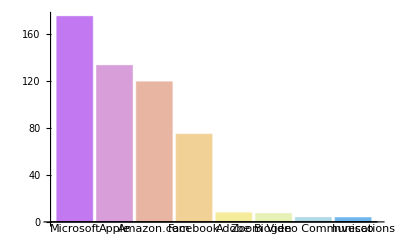

```mathematica
BarChart[H2LCurrentAssBn,ChartStyle -> "Pastel", ChartLabels -> Automatic]
```

Make a PieChart of the current assets.  Add a ChartLegends with the company names, and ChartLabels with the share of each company in %.

```mathematica
Perc = Round[H2LCurrentAssBn/Total[H2LCurrentAssBn]*100 ,0.1];
PieChart[H2LCurrentAssBn,ChartStyle -> "Pastel", ChartLegends-> Automatic,ChartLabels -> Quantity[Values[Perc],"%"]]
```

-Graphics-

Question 3:
What is the share of current assets of Microsoft?  [1 point]

```mathematica
Round[H2LCurrentAssBn[[1]]/Total[H2LCurrentAssBn]*100 ,0.1]"%"
```

33.4 %

Plot a GeoBubbleChart where each bubble is a company centered at its longitude/latitude, and the size of the bubble is the current assets of the company.

```mathematica
GeoBubbleChart[H2LCurrentAssBn]
```

-Graphics-

Question 4:
Where are located the companies with the highest current assets?  [1 point]

West America

US West Coast states

## Data acquisition (or dealing with the Dirty-Dirty Data!)

Import the CSV dataset located at this address: "https://storage.googleapis.com/mgt_492/ESG_index_companies.csv"
Store it in a variable "dataRaw" and do not display the output.
Note: Import it as a dataset, with column keys corresponding to the first row.

```mathematica
dataRaw = Import["https://storage.googleapis.com/mgt_492/ESG_index_companies.csv", "Dataset", HeaderLines -> 1];
```

Preview the dataset. Display a RandomSample of 10 rows of your dataset

```mathematica
rand = RandomSample[dataRaw, 10]
```

Extract the names of the columns (Keys) to understand what information is displayed in the dataset

```mathematica
Normal[Keys[dataRaw[[1]]]]
```

{Year,Firm,ESG controversy score,Environment controversy score,Social controvery score,Governance controversy score,Score - Emission Reduction/Biodiversity Controversies (Inactive),Score - Emission Reduction/Spill/Pollution Controversies (Inactive),Score - Product Innovation/Product Impact Controversies (Inactive),Score - Resource Reduction/Environment Impact Controversy (Inactive),Score - Client Loyalty/Anti-competition Controversy (Inactive),Score - Community/Bribery Corruption Fraud Controversies (Inactive),Score - Community/Critical Countries-Indigenous Controversy (Inactive),Score - Community/Public Health Controversies (Inactive),Score - Diversity and Opportunity/Diversity Controversies (Inactive),Score - Employment Quality/Wages Work Condition Controversy (Inactive),Score - Health & Safety/Health & Safety Controversies (Inactive),Score - Human Rights/Child Labor Controversies (Inactive),Score - Human Rights/Freedom of Association Controversies (Inactive),Score - Human Rights/Human Rights Controversies (Inactive),Score - Product Responsibility/Customer Controversies (Inactive),Score - Product Responsibility/Responsible Mrktg Controversy(Inactive),Score - Product Responsibility/Social Exclusion Controversy (Inactive),Score - Compensation Policy/Compensation Controversies (Inactive),Score - Shareholder Loyalty/Accounting Controversies (Inactive),Score - Shareholder Loyalty/Insider Dealings Controversies (Inactive),Score - Shareholder Rights/Shareholder Controversies (Inactive),mv,mc,tobin,roe,oia,ois,esg_score,esg_binaire,csr_com,csr_report,assets,roa,sg,lev,div,ind,country}

Drop the "esg_binaire", "csr_com", "csr_report" columns because they are not reliable.
Store all the remaining data in a variable "dataReliable" and do not display the output.

```mathematica
dataReliable = Normal @ KeyDrop[dataRaw,{"esg_binaire", "csr_com", "csr_report"}][Keys];
Normal[Keys[dataReliable[[1]]]]
```

Keys::invrl: The argument Year is not a valid Association or a list of rules.

Keys[{Year,Firm,ESG controversy score,Environment controversy score,Social controvery score,Governance controversy score,Score - Emission Reduction/Biodiversity Controversies (Inactive),Score - Emission Reduction/Spill/Pollution Controversies (Inactive),Score - Product Innovation/Product Impact Controversies (Inactive),Score - Resource Reduction/Environment Impact Controversy (Inactive),Score - Client Loyalty/Anti-competition Controversy (Inactive),Score - Community/Bribery Corruption Fraud Controversies (Inactive),Score - Community/Critical Countries-Indigenous Controversy (Inactive),Score - Community/Public Health Controversies (Inactive),Score - Diversity and Opportunity/Diversity Controversies (Inactive),Score - Employment Quality/Wages Work Condition Controversy (Inactive),Score - Health & Safety/Health & Safety Controversies (Inactive),Score - Human Rights/Child Labor Controversies (Inactive),Score - Human Rights/Freedom of Association Controversies (Inactive),Score - Human Rights/Human Rights Controversies (Inactive),Score - Product Responsibility/Customer Controversies (Inactive),Score - Product Responsibility/Responsible Mrktg Controversy(Inactive),Score - Product Responsibility/Social Exclusion Controversy (Inactive),Score - Compensation Policy/Compensation Controversies (Inactive),Score - Shareholder Loyalty/Accounting Controversies (Inactive),Score - Shareholder Loyalty/Insider Dealings Controversies (Inactive),Score - Shareholder Rights/Shareholder Controversies (Inactive),mv,mc,tobin,roe,oia,ois,esg_score,assets,roa,sg,lev,div,ind,country}]

Question 5:
How many columns are in the dataset "dataReliable"?  [1 point]

```mathematica
ncol=Dimensions[dataReliable][[2]]
```

41

Question 6:
What is the data type (String, Real, Integer, etc.)  of the first observation of the feature "ESG controversy score"? What about the last observation?  [1 point]
How do you interpret this result?

```mathematica
LinguisticAssistant
```

{1}[1]
 |  |  |  |

## Data Cleaning (...or your worst nightmare)

Count the number of missing values in each column. 
Note that there are two types of missing values: "" and "#DIV/0!".
Hints: 
   - One option is to map over a list of the Keys.
   - After counting the number of missing value, you can create an association between a list of keys and a list of missing values to help future operations.

```mathematica
Count[dataReliable[All,"#DIV/0!"]]
```

Count[{1}[All,#DIV/0!]]
 |  |  |  |

Question 7:
What is the number of missing values in the column "Social controvery score"?  [1 point]

```mathematica
Count[Missing[dataReliable]]
```

Count[Missing[{1}]]
 |  |  |  |

Find the four columns with the most missing values and drop them.
Store the new dataset in a variable "dataCleanCol" and do not display it.
Hint: You should expect to drop the following columns: "Environment controversy score", "Social controvery score", "Score - Emission Reduction/Spill/Pollution Controversies (Inactive)", "Score - Product Responsibility/Responsible Mrktg Controversy(Inactive)"

Delete all the rows that have at least one missing value.
Store the new dataset in a variable "dataClean" and do not display it.
Hint: One option is to use Select and FreeQ

Question 8:
How many rows does the dataset have after dropping those rows?  [1 point]

Question 9:
As you may have noted, for each company we have data for multiple years. For which year do we have more data points lefts? How many companies are in this year?  [1 point]

From now on, we will use the subset of the dataset containing the companies data only for the year with the most number of observations:
- Keep only the data for the year with the most number of observations. 
- Store this dataset in a variable "data".
- Check the dimensions of your new dataset and generate a RandomSample of 10 observations.
- Clear the variables you are not using anymore

## Data Visualization

If you could not perform the previous operations, you can answer the following questions by importing the CSV dataset "data-esg.csv" that is available in Git. Store it in a variable "data" and do not display the output. Import it as a dataset, with column keys corresponding to the first row.

```mathematica
data = Import["Assignment 1/data-esg.csv", "Dataset", HeaderLines -> 1];
```

Plot a BoxWhiskerChart of the values in the following columns "ESG controversy score", "Governance controversy score", "esg_score"

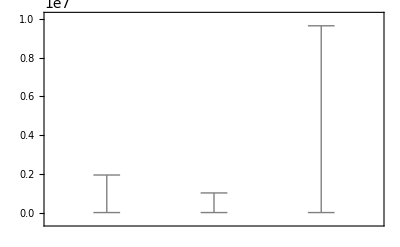

```mathematica
BoxPlot = data[[{3,4,5}]]
BoxWhiskerChart[BoxPlot]
```

Question 10:
Which between the "ESG controversy score", "Governance controversy score", "esg_score" columns has the highest median value?  [1 point]

Normalize all the columns to have values between 0 and 1, except the following ones: "Year", "Firm", "ind", "country".
Store this dataset in a variable "dataN" and do not display the result.

Question 11:
What is the normalized value for the "ESG controversy score" for the firm "1&1 DRILLISCH" for the year 2017? (round to 2 decimals, e.g., 0.50)  [1 point]

Compute the correlation matrix for the following score columns:
"ESG controversy score", 
"Governance controversy score",
"Score - Emission Reduction/Biodiversity Controversies (Inactive)", 
"Score - Community/Critical Countries-Indigenous Controversy (Inactive)",
"Score - Community/Public Health Controversies (Inactive)",
"Score - Diversity and Opportunity/Diversity Controversies (Inactive)"

Question 12:
What is the correlation between the columns "ESG controversy score" and "Governance controversy score"? (round to 2 decimals, e.g., 0.50)  [1 point]

Generate a MatrixPlot of the correlation matrix

Plot a histogram of the "assets" column (non-normalized) in order to get an idea of the distribution of the amount of assets belonging to the companies in this dataset. To make the histogram more readable use a logarithmic scale on the y-axis (x-axis are the bins of asset values).

Question 13:
What does the shape of the assets values histogram (in log scale) look like (from left to right, from smaller to larger values)? Decreasing, increasing, almost uniform, very irregular?  [1 point]

For each country, compute the number of companies and the average amount of market value ("mv" column) for the companies in the country.

Question 14:
How many companies are in country "GB"?  [1 point]
Hint: the number should be between 300-400